```mathematica
datamedical ={{1,90},{2,107},{3,126},{4,145},{5,171},{6,188},{7,189},{8,190},{9,190},{10,190},{11,192},{12,192},{13,192},{14,192},{15,203},{16,203},{17,204}}
```

{{1,90},{2,107},{3,126},{4,145},{5,171},{6,188},{7,189},{8,190},{9,190},{10,190},{11,192},{12,192},{13,192},{14,192},{15,203},{16,203},{17,204}}

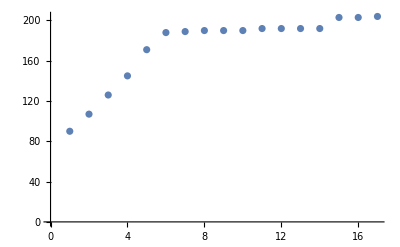

```mathematica
ListPlot[datamedical]
```

```mathematica
Limit[a(1-Exp[-r*α(1-Exp[-β*t])]),t->∞]
```

ConditionalExpression[a-a ⅇ^(-r α), (a|r|α)∈ℝ&&β>0]

```mathematica
yamadaExponential = NonlinearModelFit[datamedical,a(1-Exp[-r*α(1-Exp[-β*t])]),{{a,204},r,{α,0.2},{β,0.3}},t]
```

FittedModel[248.808 (1-ⅇ^(-1.66181 (1-«1»)))]

```mathematica
yamadaExponential["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 248.808 | 195.787 | 1.27081 | 0.226066
r | 2.87809 | 0.2372 | 12.1336 | 1.82968×10^-8
α | 0.577399 | 1.18234 | 0.488351 | 0.633435
β | 0.225336 | 0.290322 | 0.776159 | 0.451546

α  и β са незначими

yamadaExponential["BestFitParameters"]

{a→248.808,r→2.87809,α→0.577399,β→0.225336}

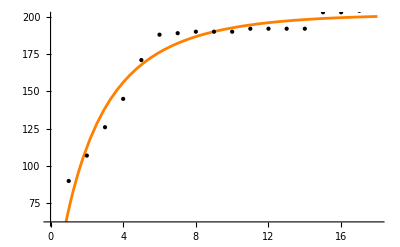

```mathematica
Plot[yamadaExponential[t],{t,0,18},Epilog-> Point[datamedical],PlotStyle->Orange]
```

```mathematica
yamadaLinear = NonlinearModelFit[datamedical,a*(1-Exp[-b t])(1-α/b)+α*a*t,{{a,204},b,α},t]
```

FittedModel[180.208 (1-ⅇ^(-0.463704 t))+1.29307 t]

```mathematica
yamadaLinear["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 182.997 | 11.3741 | 16.089 | 2.00672×10^-10
b | 0.463704 | 0.0667645 | 6.94537 | 6.81352×10^-6
α | 0.00706609 | 0.00587991 | 1.20173 | 0.249401

```mathematica
yamadaLinear["BestFitParameters"]
```

{a→182.997,b→0.463704,α→0.00706609}

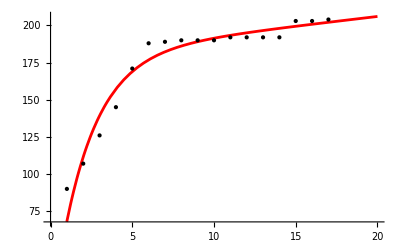

```mathematica
Plot[yamadaLinear[t],{t,0,20},Epilog->Point[datamedical],PlotStyle->Red]
```

```mathematica
yamadaExponenetialImperfect= NonlinearModelFit[datamedical,(a*b)/(α+b)(Exp[α*t]-Exp[-b*t]),{a,α,b},t]
```

FittedModel[180.881 (-ⅇ^(-0.462017 t)+ⅇ^(«21» t))]

```mathematica
yamadaExponenetialImperfect["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 183.452 | 10.7308 | 17.0958 | 8.91669×10^-11
α | 0.00656671 | 0.0050906 | 1.28997 | 0.217964
b | 0.462017 | 0.0643812 | 7.17628 | 4.73673×10^-6

```mathematica
yamadaExponenetialImperfect["BestFitParameters"]
```

{a→183.452,α→0.00656671,b→0.462017}

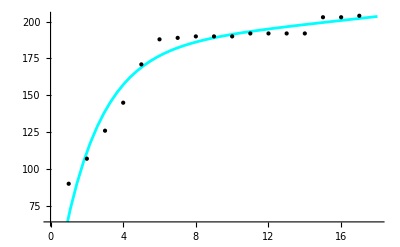

```mathematica
Plot[yamadaExponenetialImperfect[t],{t,0,18},Epilog-> Point[datamedical],PlotStyle->Cyan]
```

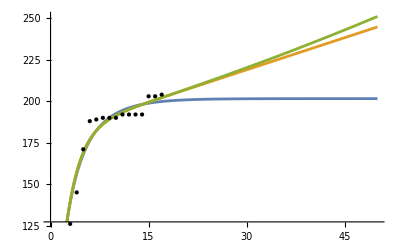

```mathematica
Plot[{yamadaExponential[t],yamadaLinear[t],yamadaExponenetialImperfect[t]},{t,0,50},Epilog->Point[datamedical],PlotStyle->{"green","blue","orange"}]
```

```mathematica
Grid[{#,yamadaExponential[#],yamadaLinear[#],yamadaExponenetialImperfect[#]}&[{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
128.603 | 132.769 | 0.998077 | 0.997485
127.489 | 130.822 | 0.997943 | 0.997502
127.487 | 130.82 | 0.997943 | 0.997502

Най- добри стойности получаваме за последния модел
-------

```mathematica
data= {{1,10},{2,12},{3,16},{4,22},{5,28},{6,36},{7,40},{8,43},{9,44},{10,50},{11,51},{12,55}}
```

{{1,10},{2,12},{3,16},{4,22},{5,28},{6,36},{7,40},{8,43},{9,44},{10,50},{11,51},{12,55}}

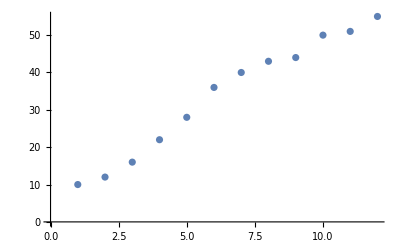

```mathematica
ListPlot[data]
```

```mathematica
goel=NonlinearModelFit[data,a(1-Exp[-b*t]),{a,b},t]
```

FittedModel[94.3479 (1-ⅇ^(-0.0732954 t))]

```mathematica
goel["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 94.3479 | 13.8142 | 6.82979 | 0.0000457025
b | 0.0732954 | 0.0150193 | 4.88009 | 0.000641877

```mathematica
goel["BestFitParameters"]
```

{a→94.3479,b→0.0732954}

```mathematica
kwang= NonlinearModelFit[data,a/(1+(a/h-1)(1+b*t)*Exp[-b*t]),{a,h,b},t]
```

FittedModel[53.8697/(1+4.87 ⅇ^(«1») (1+«19» t))]

```mathematica
kwang["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 53.8697 | 1.50575 | 35.7759 | 5.15355×10^-11
h | 9.17712 | 0.97365 | 9.42548 | 5.84224×10^-6
b | 0.605974 | 0.0396397 | 15.287 | 9.56774×10^-8

```mathematica
kwang["BestFitParameters"]
```

{a→53.8697,h→9.17712,b→0.605974}

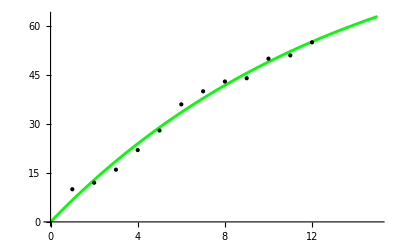

```mathematica
Plot[goel[t],{t,0,15},Epilog-> Point[data],PlotStyle->Green]
```

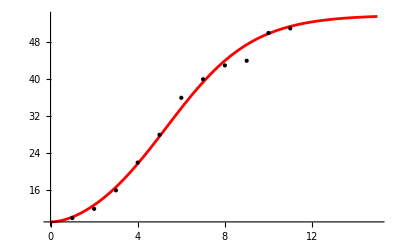

```mathematica
Plot[kwang[t],{t,0,15},Epilog->Point[data],PlotStyle->Red]
```

```mathematica
pham=NonlinearModelFit[data,a/(1+h((1+β)/(β+Exp[-b*t]))),{{a,55},b,h,β},t,Method->"Newton",MaxIterations->Infinity]
```

NonlinearModelFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FittedModel[60.7568/(1+0.522047/(«19»+ⅇ^(«1»)))]

```mathematica
pham["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 60.7568 | 0.00122084 | 49766.4 | 2.97664×10^-35
b | 32.871 | 2.40669×10^-17 | 1.36582×10^18 | 9.24873×10^-143
h | 0.314546 | 0.104174 | 3.01942 | 0.016574
β | 0.659688 | 0.0299281 | 22.0424 | 1.89497×10^-8

```mathematica
pham["BestFitParameters"]
```

{a→60.7568,b→32.871,h→0.314546,β→0.659688}

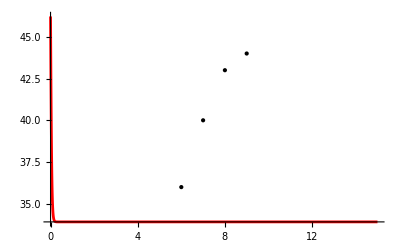

```mathematica
Plot[pham[t],{t,0,15},Epilog->Point[data],PlotStyle->Red]
```

```mathematica
haque= NonlinearModelFit[data,a/(1+β+Exp[(-b*t^α)/α]),{{a,56},b,α,β},t]
```

FittedModel[5.96986/(0.1038+ⅇ^(-«19» «1»))]

```mathematica
haque["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.96986 | 3.29536 | 1.8116 | 0.107628
b | 0.474985 | 0.177534 | 2.67546 | 0.028123
α | 0.883117 | 0.293452 | 3.00941 | 0.0168287
β | -0.8962 | 0.0632167 | -14.1766 | 5.96462×10^-7

```mathematica
haque["BestFitParameters"]
```

{a→5.96986,b→0.474985,α→0.883117,β→-0.8962}

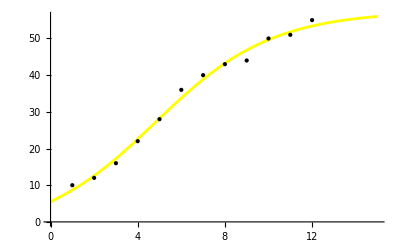

```mathematica
Plot[haque[t],{t,0,15},Epilog->Point[data],PlotStyle->Yellow]
```

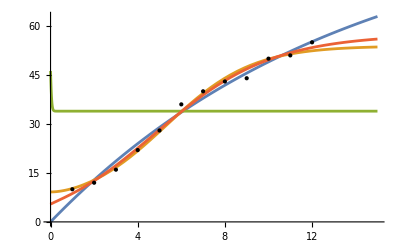

```mathematica
Plot[{goel[t],kwang[t],pham[t],haque[t]},{t,0,15},Epilog->Point[data],PlotStyle->{"Red","Green","Blue","Yellow"},PlotRange->All]
```

```mathematica
Grid[{#,goel[#],kwang[#],pham[#],haque[#]}& [{"AIC","BIC","RSquared","AdjustedRSquared"}],Frame->All]
```

AIC | BIC | RSquared | AdjustedRSquared
54.7633 | 56.218 | 0.997572 | 0.997086
52.1585 | 54.0981 | 0.998382 | 0.997842
110.224 | 112.649 | 0.832826 | 0.749238
52.1049 | 54.5295 | 0.998682 | 0.998024

На базата на статистическите тестове най- добри резултати получаваме при модела Haque

```mathematica
prediction=Table[{i,Round[haque[i]]},{i,13,60}]
```

{{13,55},{14,55},{15,56},{16,56},{17,57},{18,57},{19,57},{20,57},{21,57},{22,57},{23,57},{24,57},{25,57},{26,57},{27,57},{28,57},{29,57},{30,58},{31,58},{32,58},{33,58},{34,58},{35,58},{36,58},{37,58},{38,58},{39,58},{40,58},{41,58},{42,58},{43,58},{44,58},{45,58},{46,58},{47,58},{48,58},{49,58},{50,58},{51,58},{52,58},{53,58},{54,58},{55,58},{56,58},{57,58},{58,58},{59,58},{60,58}}

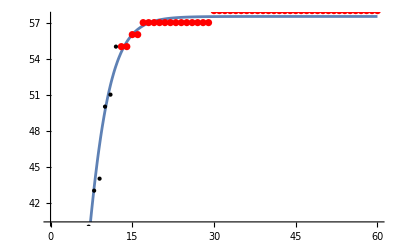

```mathematica
Show[Plot[haque[t],{t,0,60},Epilog->Point[data]],ListPlot[prediction,PlotStyle->Red]]
```